```mathematica
p1[x_]:= a1*x^3+b1*x^2+c1*x+d1
p2[x_] := a2*x^3+b2*x^2+c2*x+d2
p3[x_] := 0.5
p4[x_] := a4*x^3+b4*x^2+c4*x+d4
p5[x_] :=0.075*x-0.55
p6[x_] := a6*x^3+b6*x^2+c6*x+d6
p7[x_]:=1.25
```

```mathematica
Solve[{p1[0]==.75,p1[1/2]==1.25, p1[1]==0.5,p1'[1/2]==0},{a1,b1,c1,d1}]
```

{{a1→-1.,b1→-1.,c1→1.75,d1→0.75}}

```mathematica
p1[x_] := -1*x^3-1*x^2 + 1.75*x + 0.75
```

```mathematica
p1[x]
```

0.75+1.75 x-x^2-x^3

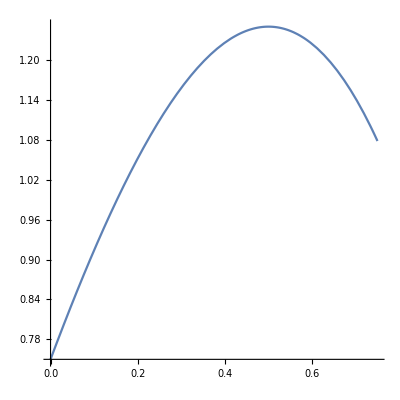

```mathematica
Plot[p1[x], {x, 0, 0.75}, AspectRatio->1]
```

```mathematica
p1[0.9]
```

0.786

```mathematica
Solve[{p2''[1]==0,p2[1]==0.5, p2'[1]==0,p2[0.9]==0.786},{a2,b2,c2,d2}]
```

{{a2→-286.,b2→858.,c2→-858.,d2→286.5}}

```mathematica
p2[x_] :=-286*x^3+858*x^2 + 858*x + 286.5
```

```mathematica
spline[x_]:= Piecewise[{{p1[x], 0≤ x< 0.9},{p2[x], 0.9≤ x≤1.1},{p3[x],1.01<x≤ 14},{p5[x],14<x≤24},{p7[x],24<x≤33.5}}]
```

```mathematica
spline[0.75]
```

1.07813

```mathematica
p5[28]
```

1.55

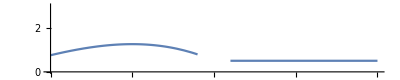

```mathematica
Plot[spline[x],{x,0,2}, AspectRatio->0.2, PlotRange->{0,3}]
```

```mathematica
f = Interpolation[{{0,0.5},{3/8,1},{3/4,0.5},{1,0.5},{2,0.5},{18,0.5},{28,1.2},{41.5,1.3}}]
```

InterpolatingFunction[…]

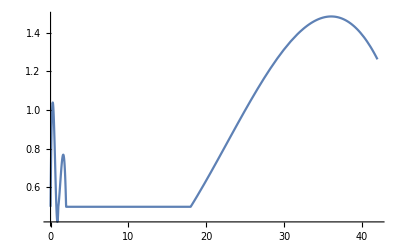

```mathematica
Plot[f[x],{x,0,42}]
```